```mathematica
hypox[a_,b_]:= (a-b)Cos[t]+b Cos[((a-b)/(b))t];
hypoy[a_,b_]:= (a-b)Sin[t]-b Sin[((a-b)/(b))t];
epix[a_,b_]:=  (a+b)Cos[t]-b Cos[((a+b)/(b))t];
epiy[a_,b_]:=  (a+b)Sin[t]-b Sin[((a+b)/(b))t];
```

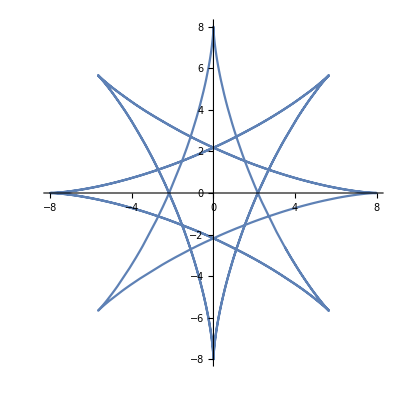

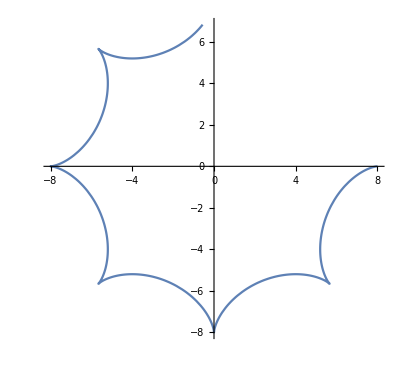

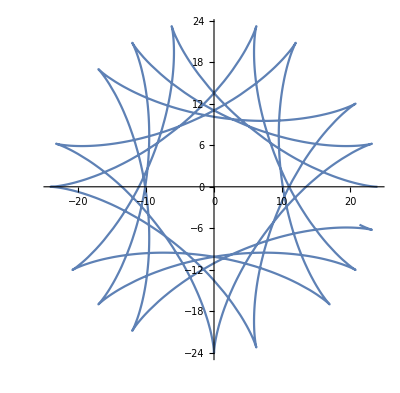

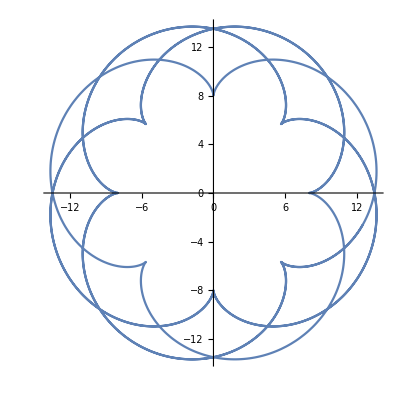

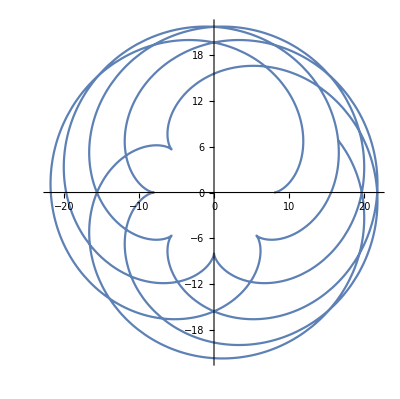

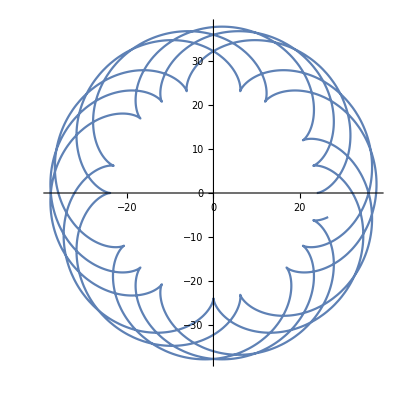

```mathematica
path = "~/Documents/LahTech/vector_calc/homework/";
g1 = ParametricPlot[{hypox[8,3],hypoy[8,3]},{t,0,10π}]
g2=ParametricPlot[{hypox[8,7],hypoy[8,7]},{t,0,10π}]
g3=ParametricPlot[{hypox[24,7],hypoy[24,7]},{t,0,10π}]
g4=ParametricPlot[{epix[8,3],epiy[8,3]},{t,0,10π}]
g5=ParametricPlot[{epix[8,7],epiy[8,7]},{t,0,10π}]
g6 =ParametricPlot[{epix[24,7],epiy[24,7]},{t,0,10π}]
Export[path <> "parap_h_83.png",g1];
Export[path <> "parap_h_87.png",g2];
Export[path <> "parap_h_247.png",g3];
Export[path <> "parap_e_83.png",g4];
Export[path <> "parap_e_87.png",g5];
Export[path <> "parap_e_247.png",g6];
```